# Impact of Parameter Perturbation on the Neural Network Performance

This project investigates the impact of perturbing parameters of a trained neural network on its performance by adding random noise to each layer. My project addresses the big question: “How resilient are neural network to perturbations or noise?” This question has an interesting implication for running neural networks where energy and computational resources are limited. 

<<RESULTS & CONCLUSION>>

## Introduction

## The LeNet Model

LeNet Model is a convolutional neural network for image classification developed by Yann LeCun and his collaborators at AT&T Bell Labs. Trained on the MNIST dataset, it is known to have achieved a significantly high performance in classifying handwritten digits with an error rate less than 1% per digit.1

```mathematica
leNet = NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<11>]

#### Architecture

LeNet comprises two main parts: the two convolutional layers with max pooling for feature extraction and the two fully connected layers for classification. Below are the summary graphics showing the architecture of the LeNet.

```mathematica
Information[leNet,"FullSummaryGraphic"]
```

-Graphics-

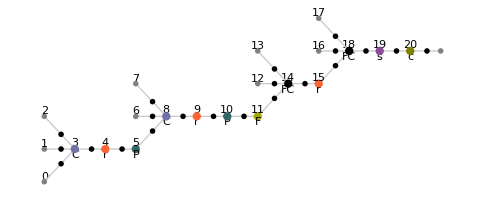

```mathematica
Information[ NetModel["LeNet Trained on MNIST Data"],"MXNetNodeGraphPlot"]
```

## The MNIST Dataset

The LeNet is was trained on the MNIST dataset of handwritten digits and is known to have achieved 98.5% accuracy on the MNIST test dataset.  The MNIST database consists of a training set of 60,000 examples and a test set of 10,000 examples.2

```mathematica
mnistTest = ResourceData["MNIST","TestData"];
```

## Exploratory Data Analysis

## Extracting the weights

We extract the weights from the LeNet for each layer. The 1st (Convolutional), 4th (Convolutional), 8th (Linear) and 10th (Linear) layers have weights.

```mathematica
layerWeights = Table[NetExtract[leNet, {n, "Weights"}], {n, {1, 4, 8, 10}}]
```

{NumericArray[…],NumericArray[…],NumericArray[<500,800>, Real32],NumericArray[…]}

## Summary Statistics of Weight Distribution

### Graphical Summary

We can plot the box plot and histogram of the weights distribution for each layer and visually analyze the center, spread, and shape of the distributions.

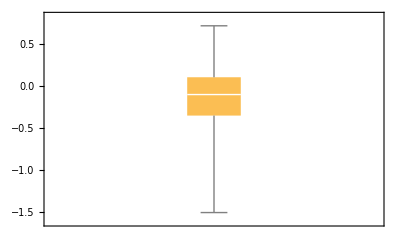
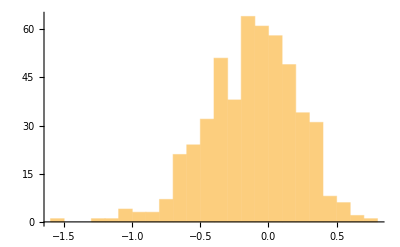
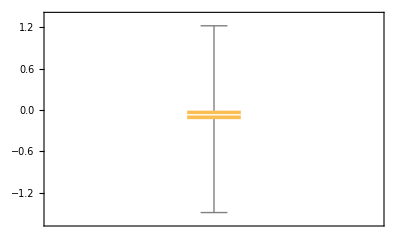
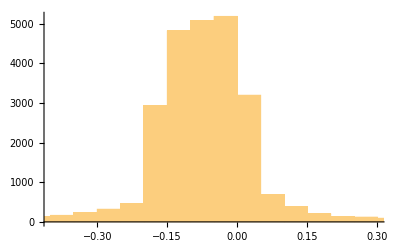
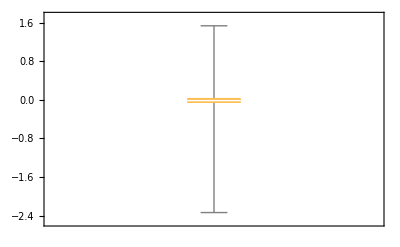
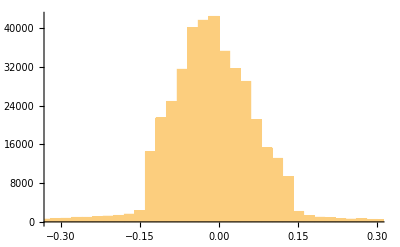
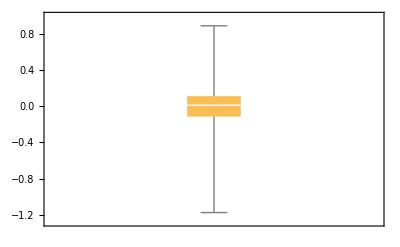
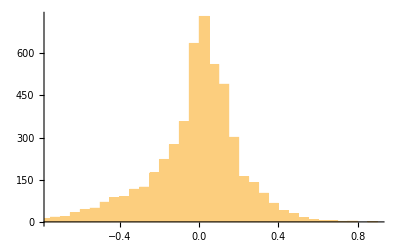
Weights Distribution
Layer 1
(Convolutional) | -Graphics- | -Graphics-
Layer 4
(Convolutional) | -Graphics- | -Graphics-
Layer 8
(Linear) | -Graphics- | -Graphics-
Layer 10
(Linear) | -Graphics- | -Graphics-

```mathematica
Grid[
{
{Style["Weights Distribution",FontSize->20, FontWeight->Bold]},
{TableForm[Table[{BoxWhiskerChart[Flatten[layerWeights[[l]]//Normal]],Histogram[Flatten[layerWeights[[l]]//Normal]]},{l,1,4}],
	TableHeadings->{{"Layer 1\n(Convolutional)","Layer 4\n(Convolutional)","Layer 8\n(Linear)","Layer 10\n(Linear)"}}]}
},
Spacings->{2,1}
]
```

### Numerical Summary

The following are the numerical summary of the weights distribution that summarizes the distribution of the weights precisely.

```mathematica
Grid[
{{Style["Weights Distribution",FontSize->20, FontWeight->Bold]},
{TableForm[Transpose[Table[
{
Mean[Flatten[layerWeights[[l]]//Normal]],
StandardDeviation[Flatten[layerWeights[[l]]//Normal]],
Min[Flatten[layerWeights[[l]]//Normal]],
Quartiles[Flatten[layerWeights[[l]]//Normal]][[1]],
Median[Flatten[layerWeights[[l]]//Normal]],
Quartiles[Flatten[layerWeights[[l]]//Normal]][[3]],
Max[Flatten[layerWeights[[l]]//Normal]],
(Max[Flatten[layerWeights[[l]]//Normal]]-Min[Flatten[layerWeights[[l]]//Normal]]),
InterquartileRange[Flatten[layerWeights[[l]]//Normal]],
Skewness[Flatten[layerWeights[[l]]//Normal]]
},
{l,1,4}
]],
TableHeadings->{{"Mean","Standard Deviation","Min","Q1/4","Median","Q3/4","Max","Range","IQR","Skewness"},{"Layer 1\n(Convolutional)","Layer 4\n(Convolutional)","Layer 8\n(Linear)","Layer 10\n(Linear)"}}
]}},
Spacings->{2,1}
]
```

Weights Distribution
 | Layer 1
(Convolutional) | Layer 4
(Convolutional) | Layer 8
(Linear) | Layer 10
(Linear)
Mean | -0.1234 | -0.075064 | -0.0162563 | -0.019502
Standard Deviation | 0.332887 | 0.150124 | 0.117813 | 0.226538
Min | -1.5101 | -1.49051 | -2.33753 | -1.17305
Q1/4 | -0.351734 | -0.134291 | -0.0650547 | -0.115114
Median | -0.10042 | -0.0711243 | -0.0159563 | 0.0103053
Q3/4 | 0.106093 | -0.0109469 | 0.0396426 | 0.110383
Max | 0.720769 | 1.22129 | 1.53562 | 0.885933
Range | 2.23087 | 2.7118 | 3.87316 | 2.05898
IQR | 0.457827 | 0.123344 | 0.104697 | 0.225497
Skewness | -0.445425 | -0.463588 | -1.44888 | -0.769615

### Analysis

Center: All layers have means and medians close to 0, which indicate that the data centered around zero with slight deviations.

Shape: As we can see from the histograms and the coefficient of skewness, the weight distributions are not symmetrical. Layer 1 (-0.457827) and 4 (-0.463588) are approximately symmetrical but slightly left-skewed shape with moderately small, negatives coefficients of skewness. On the other hand, layer 8 (-1.44888) and 10 (-0.769615)  are more left-skewed than the first two with a greater magnitude of skewness coefficient In particular, layer 8 is highly left-skewed with a coefficient significantly less than 1.  While the mean and the median of each distribution are fairly close to each other, the mean is slightly less than its median for each distribution. This is likely the result of the slight left skewness, as the extreme values pull the mean to the left side.

Spread: Layer 1 has the highest range (3.87316), which means it has the most variability overall. This is likely influenced by its skewness and the extreme values. The other three layers have fairly similar ranges. Considering the skewness of the distributions, we could use IQR to measure the variability of the data distributions. Layer 1 (0.457827) has the highest IQR, which means it has the greatest central variability.

## Adding Noise to Weights in a Neural Network

- Layer 1/4/8/10
- Gaussian/Uniform Distribution
- 1000 iterations

## Result

- Heat Map
- Plot for each layer (noise vs performance)

## Feature Representation

- Types of confusion
-

## Comparison: Fully Connected Deep Network Without Convolution

## Bibliography

1	Y. LeCun, L. Bottou, Y. Bengio, P. Haffner, "Gradient-Based Learning Applied to Document Recognition," Proceedings of the IEEE, 86(11), 2278-2324 (1998)

2	http://yann.lecun.com/exdb/mnist/